Solve for the EPs

```mathematica
<<"/home/denpak/Applications/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
alpha =5.98 - 1.07c+ 31.92w
beta = 5.56-0.25c+.38w
y=alpha+beta((x-51.04)/26.98)-((x-51.04)/26.98)^3
```

5.98-1.07 c+31.92 w

5.56-0.25 c+0.38 w

5.98-1.07 c+31.92 w+0.0370645 (5.56-0.25 c+0.38 w) (-51.04+x)-0.0000509183 (-51.04+x)^3

```mathematica
y=alpha+beta x-(x)^3
```

5.98-1.07 c+31.92 w+(5.56-0.25 c+0.38 w) x-x^3

```mathematica
y//Simplify
```

5.98-1.07 c+31.92 w+(5.56-0.25 c+0.38 w) x-x^3

```mathematica
Manipulate[Plot[y,{x,-2.0101,2.0101}],{f,0,200},{g,0,200}]
```

```mathematica
S= Solve[y==0,x,Reals]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
s
```

51.04-((1.67989×10^-8-2.90966×10^-8 ⅈ) (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g))/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)+(1.05827×10^-8+1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)

```mathematica
Plot3D[{x/.S[[1]],x/.S[[2]],x/.S[[3]]},{f,0,30},{g,0,0.4}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Re[FullSimplify[x/.S[[2]],{f∈Reals,g∈Reals }]]
```

Re[((0.00629961+0.0109112 ⅈ) (556.-25. f+38. g))/((-161.46+28.89 f-861.84 g+√(1.6875 (-22.24+1. f-1.52 g)^3+(161.46-28.89 f+861.84 g)^2))^(1/3))+(0.132283-0.229122 ⅈ) (-161.46+28.89 f-861.84 g+√(1.6875 (-22.24+1. f-1.52 g)^3+(161.46-28.89 f+861.84 g)^2))^(1/3)]

```mathematica
Expand[%50]
```

51.04+(3.187×10^10-5.52005×10^10 ⅈ)/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)-((1.433×10^9-2.48203×10^9 ⅈ) f)/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)+((2.17817×10^9-3.77269×10^9 ⅈ) g)/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)+(1.05827×10^-8+1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)

```mathematica
Simplify[E^Sin[x]∈PositiveReals,]
```

51.04-((1.67989×10^-8-2.90966×10^-8 ⅈ) (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g))/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)+(1.05827×10^-8+1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)

```mathematica
Re[Evaluate[s]]
```

51.04+Re[-(((1.67989×10^-8-2.90966×10^-8 ⅈ) (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g))/(-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3))+(1.05827×10^-8+1.83297×10^-8 ⅈ) (-6.19328×10^27+1.10816×10^27 f-3.30585×10^28 g+√(4. (-1.89714×10^18+8.53032×10^16 f-1.29661×10^17 g)^3+(6.19328×10^27-1.10816×10^27 f+3.30585×10^28 g)^2))^(1/3)]

```mathematica
Plot3D[s,{f,0,18},{g,0,0.5},MaxRecursion->5,PlotStyle->Green,AxesLabel->{"c","w","y"}]
```

-Graphics3D-

```mathematica
p=-Graphics3D-
```

-Graphics3D-

```mathematica
x/.S[[2]]
```

((0.00629961+0.0109112 ⅈ) (556.-25. f+38. g))/((-161.46+28.89 f-861.84 g+√(1.6875 (-22.24+1. f-1.52 g)^3+(161.46-28.89 f+861.84 g)^2))^(1/3))+(0.132283-0.229122 ⅈ) (-161.46+28.89 f-861.84 g+√(1.6875 (-22.24+1. f-1.52 g)^3+(161.46-28.89 f+861.84 g)^2))^(1/3)

```mathematica
p2=Plot3D[y=50,{c,0,18},{g,0,0.5},PlotStyle->RGBColor[0.51,0.51,1.],AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{(4 -( x/.S[[2]]))/8},{f,0,20},{g,0,0.5}]
```

-Graphics3D-

```mathematica
RGBColor[84/255,180/255,53/255]
```

RGBColor[Rational[28, 85], Rational[12, 17], Rational[53, 255]]

```mathematica
ColorSetter[RGBColor[84/255,180/2550,53]]
```

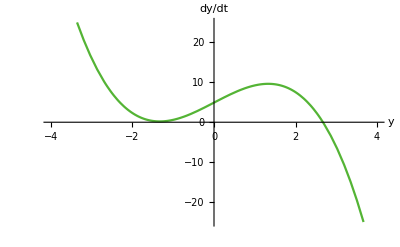
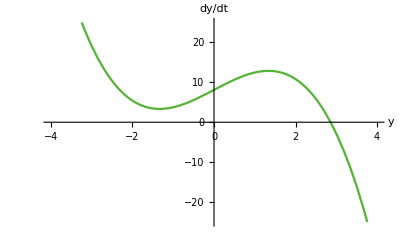
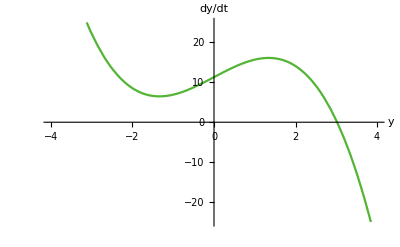
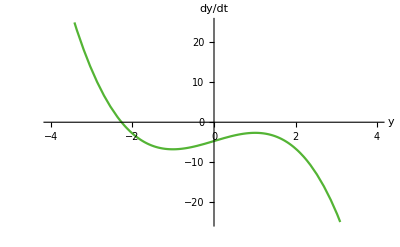
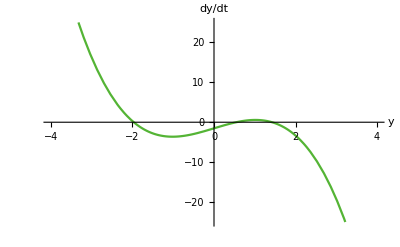
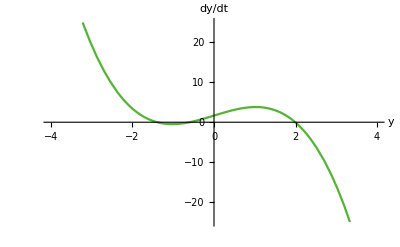
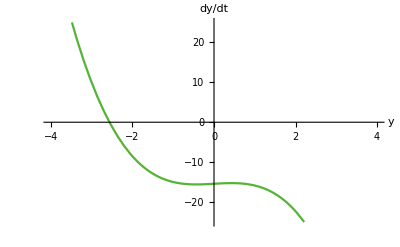
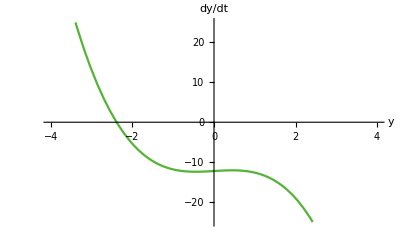

tmp.png

```mathematica
plots=Table[Plot[5.98-1.07 f+31.92 g+(5.56-0.25 f+0.38 g) x-x^3,{x,-4.0101010101010102,4.0101010101010102},PlotStyle->RGBColor[57/255,181/255,224/255],AxesLabel->{"y","dy/dt"},PlotRange->{-25,25}],{f,{1,10,20}},{g,{0,0.1,0.2}}]
imgs=Transpose@plots;
g=Graphics[MapIndexed[Inset[#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->{{{1,"1"},{2,"10"},{3,"20"}},{{1-0.05,"0"},{2-0.05,"0.1"},{3-0.05,"0.2"}}},AxesStyle->{{Thick,Arrowheads[0.03]},{Thick,Arrowheads[0.03]}},AxesOrigin->{1/4,1/4},ImageSize->700];
Export["tmp.png",Labeled[%,{"Arm Circumference","Arm Weight"},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[Gray, Medium,FontFamily->"Helvetica",FontSize->15]]]
```

```mathematica
.18
```

```mathematica
Manipulate[Plot[y,{x,-.01,.01}],{f,0,1},{g,0,1}]
```

```mathematica
Solve[5.98-10.7 f+31.92 g+0.037064492216456635 (5.56-0.25 f+0.38 g) (-51.04+x)-0.00005091833147753056 (-51.04+x)^3==0/.{f->2.095,g->15},x]
```

{{x→-59.5096-169.849 ⅈ},{x→-59.5096+169.849 ⅈ},{x→272.139}}

```mathematica
plots=Table[Plot[5.98-10.7 f+31.92 g+0.037064492216456635 (5.56-0.25 f+0.38 g) (-51.04+x)-0.00005091833147753056 (-51.04+x)^3,{x,-0.1,0.1}],{f,0,20,2},{g,0,20,2}]
imgs=Transpose@plots;
Graphics[MapIndexed[Inset[Rasterize@#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->Range@Dimensions@imgs,AxesStyle->Arrowheads[0.03],AxesOrigin->{1/4,1/4},ImageSize->700];

Labeled[%,{"Beta","Alpha"},{Left,Bottom},RotateLabel->True]
```

```mathematica
""
```

```mathematica
ds = DynamicalSystem[y,{{x,-10,10}},{{f,0,100},{g,100,500}}]
alpha + beta
```

DynamicalSystem[5.98-10.7 f+31.92 g+0.0370645 (5.56-0.25 f+0.38 g) (-51.04+x)-0.0000509183 (-51.04+x)^3,{{x,-10,10}},{{f,0,100},{g,100,500}}]

11.54-10.95 f+32.3 g

Plot that branch with higher resolution

Let’s compute the central slope of this curve as a function of d

```mathematica
l2 =Plot[0.2745781780866053-1.9083893773871397 c,{c,-4,4},PlotPoints->300]
```

```mathematica
Solve[s==50]
```

$Aborted